```mathematica
i1=13552(*柱子转动惯量*)
i2=202.75(*锥体转动惯量*)
ii=7001.914(*纵摇附加转动惯量*)
eta0=250000(*弹簧扭转刚度*)
eta1=654.3383(*纵摇兴波阻尼系数*)
eta2=8890.7(*静水恢复力矩系数*)
nu2=1000(*旋转阻尼器的阻尼系数*)
l=7001.914(*附加转动惯量*)
omega=1.7152
```

13552

202.75

7001.91

250000

654.338

8890.7

1000

7001.91

1.7152

```mathematica
(*Theta -> y*)
eq1=i2*y2''[t]+eta0*(y2[t]+y1[t])+nu2*(y1'[t]+y2'[t])==0
```

250000 (y1[t]+y2[t])+1000 (y1'[t]+y2'[t])+202.75 y2''[t]==0

```mathematica
eq2=(i1+ii)*y1''[t]+eta0*(y1[t]+y2[t])+nu2*(y1'[t]+y2'[t])+eta2*y1[t]+eta1*y1'[t]==l*Cos[omega*t]
```

8890.7 y1[t]+250000 (y1[t]+y2[t])+654.338 y1'[t]+1000 (y1'[t]+y2'[t])+20553.9 y1''[t]==7001.91 Cos[1.7152 t]

```mathematica
sol=NDSolve[{eq1,eq2,y1[0]==0,y1'[0]==0,y2[0]==0,y2'[0]==0},{y1[t],y2[t]},{t,0,100}]
```

{{y1[t]→InterpolatingFunction[…][t],y2[t]→InterpolatingFunction[…][t]}}

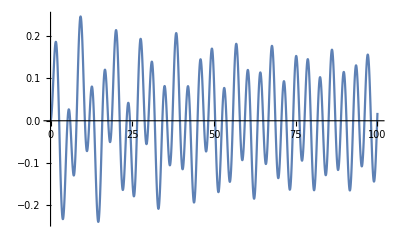

```mathematica
Plot[y1[t]/.sol,{t,0,100}]
```

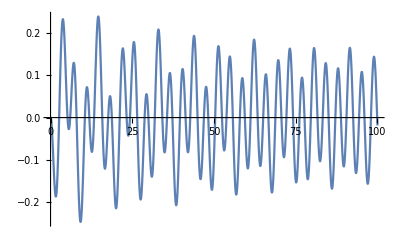

```mathematica
Plot[y2[t]/.sol,{t,0,100}]
```